# Drugi kviz

Vsaka podnaloga je vredna 1 točko, razen če je pri podnalogi zapisano drugače. Skupno je moč doseči 20 točk.

## Naloga 1

a)  Definite funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi produkt indeksa stolpca in indeksa vrstice (začnemo šteti z 1).

```mathematica
A[n_,m_] :=Table[i+j, {i,1,n},{j,1,m}]
```

b) Pokažite, da je  simetrična matrika.

```mathematica
A[n_]:=Table[i*j,{i,1,n},{j,1,n}]
MatrixQ[A[5]==Transpose[A[5]]]
```

False

c) Izračunajte lastne vrednosti in lastne vektorje matrike .

```mathematica
Eigenvalues[A[10,10]]
Eigenvectors[A[10,10]]
```

{5 (11+√154),5 (11-√154),0,0,0,0,0,0,0,0}

{{-(-150258053-12108139 √154)/(337954529+27233152 √154),(3 (57037739+4596232 √154))/(337954529+27233152 √154),-(-191968381-15469253 √154)/(337954529+27233152 √154),(5 (42564709+3429962 √154))/(337954529+27233152 √154),(27 (8654767+697421 √154))/(337954529+27233152 √154),-(-254533873-20510924 √154)/(337954529+27233152 √154),-(-275389037-22191481 √154)/(337954529+27233152 √154),(3 (98748067+7957346 √154))/(337954529+27233152 √154),(5 (63419873+5110519 √154))/(337954529+27233152 √154),1},{-(150258053-12108139 √154)/(-337954529+27233152 √154),(3 (-57037739+4596232 √154))/(-337954529+27233152 √154),-(191968381-15469253 √154)/(-337954529+27233152 √154),(5 (-42564709+3429962 √154))/(-337954529+27233152 √154),(27 (-8654767+697421 √154))/(-337954529+27233152 √154),-(254533873-20510924 √154)/(-337954529+27233152 √154),-(275389037-22191481 √154)/(-337954529+27233152 √154),(3 (-98748067+7957346 √154))/(-337954529+27233152 √154),(5 (-63419873+5110519 √154))/(-337954529+27233152 √154),1},{8,-9,0,0,0,0,0,0,0,1},{7,-8,0,0,0,0,0,0,1,0},{6,-7,0,0,0,0,0,1,0,0},{5,-6,0,0,0,0,1,0,0,0},{4,-5,0,0,0,1,0,0,0,0},{3,-4,0,0,1,0,0,0,0,0},{2,-3,0,1,0,0,0,0,0,0},{1,-2,1,0,0,0,0,0,0,0}}

d) Izračunajte karakteristični polinom matrike .

```mathematica
CharacteristicPolynomial[A[10,10],x]
```

-825 x^8-110 x^9+x^10

e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .

```mathematica
G = DiagonalMatrix[Eigenvalues[A[10,10]]]
P = Transpose[Eigenvectors[A[10,10]]]
Inverse [P]
```

{{5 (11+√154),0,0,0,0,0,0,0,0,0},{0,5 (11-√154),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

{{-(-150258053-12108139 √154)/(337954529+27233152 √154),-(150258053-12108139 √154)/(-337954529+27233152 √154),8,7,6,5,4,3,2,1},{(3 (57037739+4596232 √154))/(337954529+27233152 √154),(3 (-57037739+4596232 √154))/(-337954529+27233152 √154),-9,-8,-7,-6,-5,-4,-3,-2},{-(-191968381-15469253 √154)/(337954529+27233152 √154),-(191968381-15469253 √154)/(-337954529+27233152 √154),0,0,0,0,0,0,0,1},{(5 (42564709+3429962 √154))/(337954529+27233152 √154),(5 (-42564709+3429962 √154))/(-337954529+27233152 √154),0,0,0,0,0,0,1,0},{(27 (8654767+697421 √154))/(337954529+27233152 √154),(27 (-8654767+697421 √154))/(-337954529+27233152 √154),0,0,0,0,0,1,0,0},{-(-254533873-20510924 √154)/(337954529+27233152 √154),-(254533873-20510924 √154)/(-337954529+27233152 √154),0,0,0,0,1,0,0,0},{-(-275389037-22191481 √154)/(337954529+27233152 √154),-(275389037-22191481 √154)/(-337954529+27233152 √154),0,0,0,1,0,0,0,0},{(3 (98748067+7957346 √154))/(337954529+27233152 √154),(3 (-98748067+7957346 √154))/(-337954529+27233152 √154),0,0,1,0,0,0,0,0},{(5 (63419873+5110519 √154))/(337954529+27233152 √154),(5 (-63419873+5110519 √154))/(-337954529+27233152 √154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}}

{{(9-9663743364/(-337954529+27233152 √154)+(778726632 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8-7560634983/(-337954529+27233152 √154)+(609253329 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7-5457526602/(-337954529+27233152 √154)+(439780026 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(6-3354418221/(-337954529+27233152 √154)+(270306723 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(5-1251309840/(-337954529+27233152 √154)+(100833420 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(4+851798541/(-337954529+27233152 √154)-(68639883 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(3+2954906922/(-337954529+27233152 √154)-(238113186 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(2+5058015303/(-337954529+27233152 √154)-(407586489 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(1+7161123684/(-337954529+27233152 √154)-(577059792 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))},{(-9-9663743364/(337954529+27233152 √154)-(778726632 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-8-7560634983/(337954529+27233152 √154)-(609253329 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-7-5457526602/(337954529+27233152 √154)-(439780026 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-6-3354418221/(337954529+27233152 √154)-(270306723 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-5-1251309840/(337954529+27233152 √154)-(100833420 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-4+851798541/(337954529+27233152 √154)+(68639883 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-3+2954906922/(337954529+27233152 √154)+(238113186 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2+5058015303/(337954529+27233152 √154)+(407586489 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1+7161123684/(337954529+27233152 √154)+(577059792 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))},{(9663743364/(-337954529+27233152 √154)-(778726632 √154)/(-337954529+27233152 √154)+9663743364/(337954529+27233152 √154)+(778726632 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7560634983/(-337954529+27233152 √154)-(609253329 √154)/(-337954529+27233152 √154)+7560634983/(337954529+27233152 √154)+(609253329 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(5457526602/(-337954529+27233152 √154)-(439780026 √154)/(-337954529+27233152 √154)+5457526602/(337954529+27233152 √154)+(439780026 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(3354418221/(-337954529+27233152 √154)-(270306723 √154)/(-337954529+27233152 √154)+3354418221/(337954529+27233152 √154)+(270306723 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(1251309840/(-337954529+27233152 √154)-(100833420 √154)/(-337954529+27233152 √154)+1251309840/(337954529+27233152 √154)+(100833420 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-851798541/(-337954529+27233152 √154)+(68639883 √154)/(-337954529+27233152 √154)-851798541/(337954529+27233152 √154)-(68639883 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2954906922/(-337954529+27233152 √154)+(238113186 √154)/(-337954529+27233152 √154)-2954906922/(337954529+27233152 √154)-(238113186 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-5058015303/(-337954529+27233152 √154)+(407586489 √154)/(-337954529+27233152 √154)-5058015303/(337954529+27233152 √154)-(407586489 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-7161123684/(-337954529+27233152 √154)+(577059792 √154)/(-337954529+27233152 √154)-7161123684/(337954529+27233152 √154)-(577059792 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),-((1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))))},{(-2853894285/(-337954529+27233152 √154)+(229973355 √154)/(-337954529+27233152 √154)-2853894285/(337954529+27233152 √154)-(229973355 √154)/(337954529+27233152 √154)-(303118200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2536794920/(-337954529+27233152 √154)+(204420760 √154)/(-337954529+27233152 √154)-2536794920/(337954529+27233152 √154)-(204420760 √154)/(337954529+27233152 √154)-(173210400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2219695555/(-337954529+27233152 √154)+(178868165 √154)/(-337954529+27233152 √154)-2219695555/(337954529+27233152 √154)-(178868165 √154)/(337954529+27233152 √154)-(43302600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1902596190/(-337954529+27233152 √154)+(153315570 √154)/(-337954529+27233152 √154)-1902596190/(337954529+27233152 √154)-(153315570 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1585496825/(-337954529+27233152 √154)+(127762975 √154)/(-337954529+27233152 √154)-1585496825/(337954529+27233152 √154)-(127762975 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1268397460/(-337954529+27233152 √154)+(102210380 √154)/(-337954529+27233152 √154)-1268397460/(337954529+27233152 √154)-(102210380 √154)/(337954529+27233152 √154)+(346420800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-951298095/(-337954529+27233152 √154)+(76657785 √154)/(-337954529+27233152 √154)-951298095/(337954529+27233152 √154)-(76657785 √154)/(337954529+27233152 √154)+(476328600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-634198730/(-337954529+27233152 √154)+(51105190 √154)/(-337954529+27233152 √154)-634198730/(337954529+27233152 √154)-(51105190 √154)/(337954529+27233152 √154)+(606236400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8947132700/(-337954529+27233152 √154)-(720980500 √154)/(-337954529+27233152 √154)+8947132700/(337954529+27233152 √154)+(720980500 √154)/(337954529+27233152 √154)-(1212472800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(866052000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2666197809/(-337954529+27233152 √154)+(214848342 √154)/(-337954529+27233152 √154)-2666197809/(337954529+27233152 √154)-(214848342 √154)/(337954529+27233152 √154)-(173210400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2369953608/(-337954529+27233152 √154)+(190976304 √154)/(-337954529+27233152 √154)-2369953608/(337954529+27233152 √154)-(190976304 √154)/(337954529+27233152 √154)-(75779550 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2073709407/(-337954529+27233152 √154)+(167104266 √154)/(-337954529+27233152 √154)-2073709407/(337954529+27233152 √154)-(167104266 √154)/(337954529+27233152 √154)+(21651300 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1777465206/(-337954529+27233152 √154)+(143232228 √154)/(-337954529+27233152 √154)-1777465206/(337954529+27233152 √154)-(143232228 √154)/(337954529+27233152 √154)+(119082150 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1481221005/(-337954529+27233152 √154)+(119360190 √154)/(-337954529+27233152 √154)-1481221005/(337954529+27233152 √154)-(119360190 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1184976804/(-337954529+27233152 √154)+(95488152 √154)/(-337954529+27233152 √154)-1184976804/(337954529+27233152 √154)-(95488152 √154)/(337954529+27233152 √154)+(313943850 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-888732603/(-337954529+27233152 √154)+(71616114 √154)/(-337954529+27233152 √154)-888732603/(337954529+27233152 √154)-(71616114 √154)/(337954529+27233152 √154)+(411374700 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8671743663/(-337954529+27233152 √154)-(698789019 √154)/(-337954529+27233152 √154)+8671743663/(337954529+27233152 √154)+(698789019 √154)/(337954529+27233152 √154)-(1439811450 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-296244201/(-337954529+27233152 √154)+(23872038 √154)/(-337954529+27233152 √154)-296244201/(337954529+27233152 √154)-(23872038 √154)/(337954529+27233152 √154)+(606236400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(703667250 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2478501333/(-337954529+27233152 √154)+(199723329 √154)/(-337954529+27233152 √154)-2478501333/(337954529+27233152 √154)-(199723329 √154)/(337954529+27233152 √154)-(43302600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2203112296/(-337954529+27233152 √154)+(177531848 √154)/(-337954529+27233152 √154)-2203112296/(337954529+27233152 √154)-(177531848 √154)/(337954529+27233152 √154)+(21651300 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1927723259/(-337954529+27233152 √154)+(155340367 √154)/(-337954529+27233152 √154)-1927723259/(337954529+27233152 √154)-(155340367 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1652334222/(-337954529+27233152 √154)+(133148886 √154)/(-337954529+27233152 √154)-1652334222/(337954529+27233152 √154)-(133148886 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1376945185/(-337954529+27233152 √154)+(110957405 √154)/(-337954529+27233152 √154)-1376945185/(337954529+27233152 √154)-(110957405 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1101556148/(-337954529+27233152 √154)+(88765924 √154)/(-337954529+27233152 √154)-1101556148/(337954529+27233152 √154)-(88765924 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8438064954/(-337954529+27233152 √154)-(679958652 √154)/(-337954529+27233152 √154)+8438064954/(337954529+27233152 √154)+(679958652 √154)/(337954529+27233152 √154)-(1602196200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-550778074/(-337954529+27233152 √154)+(44382962 √154)/(-337954529+27233152 √154)-550778074/(337954529+27233152 √154)-(44382962 √154)/(337954529+27233152 √154)+(411374700 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-275389037/(-337954529+27233152 √154)+(22191481 √154)/(-337954529+27233152 √154)-275389037/(337954529+27233152 √154)-(22191481 √154)/(337954529+27233152 √154)+(476328600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(541282500 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2290804857/(-337954529+27233152 √154)+(184598316 √154)/(-337954529+27233152 √154)-2290804857/(337954529+27233152 √154)-(184598316 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2036270984/(-337954529+27233152 √154)+(164087392 √154)/(-337954529+27233152 √154)-2036270984/(337954529+27233152 √154)-(164087392 √154)/(337954529+27233152 √154)+(119082150 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1781737111/(-337954529+27233152 √154)+(143576468 √154)/(-337954529+27233152 √154)-1781737111/(337954529+27233152 √154)-(143576468 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1527203238/(-337954529+27233152 √154)+(123065544 √154)/(-337954529+27233152 √154)-1527203238/(337954529+27233152 √154)-(123065544 √154)/(337954529+27233152 √154)+(184036050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1272669365/(-337954529+27233152 √154)+(102554620 √154)/(-337954529+27233152 √154)-1272669365/(337954529+27233152 √154)-(102554620 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8246096573/(-337954529+27233152 √154)-(664489399 √154)/(-337954529+27233152 √154)+8246096573/(337954529+27233152 √154)+(664489399 √154)/(337954529+27233152 √154)-(1699627050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-763601619/(-337954529+27233152 √154)+(61532772 √154)/(-337954529+27233152 √154)-763601619/(337954529+27233152 √154)-(61532772 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-509067746/(-337954529+27233152 √154)+(41021848 √154)/(-337954529+27233152 √154)-509067746/(337954529+27233152 √154)-(41021848 √154)/(337954529+27233152 √154)+(313943850 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-254533873/(-337954529+27233152 √154)+(20510924 √154)/(-337954529+27233152 √154)-254533873/(337954529+27233152 √154)-(20510924 √154)/(337954529+27233152 √154)+(346420800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(378897750 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2103108381/(-337954529+27233152 √154)+(169473303 √154)/(-337954529+27233152 √154)-2103108381/(337954529+27233152 √154)-(169473303 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1869429672/(-337954529+27233152 √154)+(150642936 √154)/(-337954529+27233152 √154)-1869429672/(337954529+27233152 √154)-(150642936 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1635750963/(-337954529+27233152 √154)+(131812569 √154)/(-337954529+27233152 √154)-1635750963/(337954529+27233152 √154)-(131812569 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1402072254/(-337954529+27233152 √154)+(112982202 √154)/(-337954529+27233152 √154)-1402072254/(337954529+27233152 √154)-(112982202 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8095838520/(-337954529+27233152 √154)-(652381260 √154)/(-337954529+27233152 √154)+8095838520/(337954529+27233152 √154)+(652381260 √154)/(337954529+27233152 √154)-(1732104000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-934714836/(-337954529+27233152 √154)+(75321468 √154)/(-337954529+27233152 √154)-934714836/(337954529+27233152 √154)-(75321468 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-701036127/(-337954529+27233152 √154)+(56491101 √154)/(-337954529+27233152 √154)-701036127/(337954529+27233152 √154)-(56491101 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-467357418/(-337954529+27233152 √154)+(37660734 √154)/(-337954529+27233152 √154)-467357418/(337954529+27233152 √154)-(37660734 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-233678709/(-337954529+27233152 √154)+(18830367 √154)/(-337954529+27233152 √154)-233678709/(337954529+27233152 √154)-(18830367 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-1915411905/(-337954529+27233152 √154)+(154348290 √154)/(-337954529+27233152 √154)-1915411905/(337954529+27233152 √154)-(154348290 √154)/(337954529+27233152 √154)+(346420800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1702588360/(-337954529+27233152 √154)+(137198480 √154)/(-337954529+27233152 √154)-1702588360/(337954529+27233152 √154)-(137198480 √154)/(337954529+27233152 √154)+(313943850 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1489764815/(-337954529+27233152 √154)+(120048670 √154)/(-337954529+27233152 √154)-1489764815/(337954529+27233152 √154)-(120048670 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7987290795/(-337954529+27233152 √154)-(643634235 √154)/(-337954529+27233152 √154)+7987290795/(337954529+27233152 √154)+(643634235 √154)/(337954529+27233152 √154)-(1699627050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1064117725/(-337954529+27233152 √154)+(85749050 √154)/(-337954529+27233152 √154)-1064117725/(337954529+27233152 √154)-(85749050 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-851294180/(-337954529+27233152 √154)+(68599240 √154)/(-337954529+27233152 √154)-851294180/(337954529+27233152 √154)-(68599240 √154)/(337954529+27233152 √154)+(184036050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-638470635/(-337954529+27233152 √154)+(51449430 √154)/(-337954529+27233152 √154)-638470635/(337954529+27233152 √154)-(51449430 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-425647090/(-337954529+27233152 √154)+(34299620 √154)/(-337954529+27233152 √154)-425647090/(337954529+27233152 √154)-(34299620 √154)/(337954529+27233152 √154)+(119082150 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-212823545/(-337954529+27233152 √154)+(17149810 √154)/(-337954529+27233152 √154)-212823545/(337954529+27233152 √154)-(17149810 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(54128250 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-1727715429/(-337954529+27233152 √154)+(139223277 √154)/(-337954529+27233152 √154)-1727715429/(337954529+27233152 √154)-(139223277 √154)/(337954529+27233152 √154)+(476328600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1535747048/(-337954529+27233152 √154)+(123754024 √154)/(-337954529+27233152 √154)-1535747048/(337954529+27233152 √154)-(123754024 √154)/(337954529+27233152 √154)+(411374700 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7920453398/(-337954529+27233152 √154)-(638248324 √154)/(-337954529+27233152 √154)+7920453398/(337954529+27233152 √154)+(638248324 √154)/(337954529+27233152 √154)-(1602196200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1151810286/(-337954529+27233152 √154)+(92815518 √154)/(-337954529+27233152 √154)-1151810286/(337954529+27233152 √154)-(92815518 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-959841905/(-337954529+27233152 √154)+(77346265 √154)/(-337954529+27233152 √154)-959841905/(337954529+27233152 √154)-(77346265 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-767873524/(-337954529+27233152 √154)+(61877012 √154)/(-337954529+27233152 √154)-767873524/(337954529+27233152 √154)-(61877012 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-575905143/(-337954529+27233152 √154)+(46407759 √154)/(-337954529+27233152 √154)-575905143/(337954529+27233152 √154)-(46407759 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-383936762/(-337954529+27233152 √154)+(30938506 √154)/(-337954529+27233152 √154)-383936762/(337954529+27233152 √154)-(30938506 √154)/(337954529+27233152 √154)+(21651300 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-191968381/(-337954529+27233152 √154)+(15469253 √154)/(-337954529+27233152 √154)-191968381/(337954529+27233152 √154)-(15469253 √154)/(337954529+27233152 √154)-(43302600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),-((108256500 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))))}}

f) (2 točki) Rešite matrično enačbo .

```mathematica
X=LinearSolve[A[10,10]+P-G , IdentityMatrix[10]]
```

LinearSolve[-G+P+A[10,10],{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}]

g) Ali je matrika  obrnljiva?

```mathematica
A[n_]:=Table[i*j,{i,1,n},{j,1,n}];
Det[A[10]] 
MatrixRank[A[10]]
```

0

1

## Naloga 2

Imamo klančino z naklonom 20 stopinj dolžine 5m. Na dnu klančine se nahaja ravnina dolžine 10m.
Kroglico z radijem 20cm potisnemo s skrajno desnega roba ravnine s hitrostjo v0 = 11m/s. Ko pride kroglica na vrh klančine, skoči čez rob, dokler ne pristane na tleh (poševni met). 
Predpostavite lahko, da med kroglico in podlago ni trenja in da se zaradi kotaljenja energija ne izgublja. Simulirajte gibanje kroglice do trenutka ko pristane na tleh.
Za gravitacijski pospešek vzemite g = 9.81 m/s^2, za simulacijo pa vzemite  . (Glej sliko).

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, dolžino podlage, začetno hitrost in radij kroglice.

```mathematica
g=9.81;
kot=20 Degree;
d=10;
v0=11;
r=0.2;
```

b) Nariši klančino in tla.

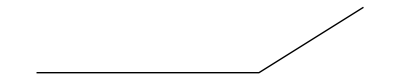

```mathematica
kot=20 Degree;
dKlanec=5;
dRavnina=10;

Graphics[Line[{{0,0},{dRavnina,0},{dRavnina+dKlanec*Cos[kot],dKlanec*Sin[kot]}  }]]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče (Uporabi `Dynamic`).

```mathematica
kot=20 Degree;
dRavnina=10;
dKlanec=5;
r=0.2;

DynamicModule[{x=0},Column[{Slider[Dynamic[x],{0,dRavnina+dKlanec*Cos[kot]}],Dynamic[Graphics[{Line[{{0,0},{dRavnina,0},{dRavnina+dKlanec*Cos[kot],dKlanec*Sin[kot]}}],Red,Disk[{x,If[x<=dRavnina,r,r+(x-dRavnina)*Tan[kot]]},r]},PlotRange->{{0,dRavnina+dKlanec*Cos[kot]+1},{-1,dKlanec*Sin[kot]+1}},Axes->True,AspectRatio->0.3,AxesLabel->{"x","y"}]]}]]
```

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
dRavnina=10;

naKlancu[{x_,y_}]:=x>dRavnina
```

e) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α po času Δt.

```mathematica
posodobiHitrost[v_,a_]:={v[[1]]+g*t/Tan[a],v[[2]]-g*t};
```

f) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostNaKlanec[v_,a_]:={v[[1]]*Cos[a],Abs[v[[1]]*Sin[a]]}
```

g) Definiraj funkcijo `posodobiHitrostPosevniMet`, ki sprejme trenutno hitrost kroglice in vrne novo hitrost kroglice po času Δt.

```mathematica
g=9.81; 

posodobiHitrostPosevniMet[v_,deltaT_]:={v[[1]],v[[2]]-g*deltaT}
```

h) Definiraj funkcijo `posodobiLego`, ki sprejme trenutno lego kroglice in njeno hitrost in vrne novo lego kroglice po času Δt.

```mathematica
posodobiLego[r_,v_,deltaT_]:=r+deltaT*v
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice. (4 točke - gibanje po ravnini (1 točka), gibanje po klančini (1 točka), gibanje pri poševnem metu (1 točka), simulacija se ustavi, ko žogica pristane na tleh (1 točka))

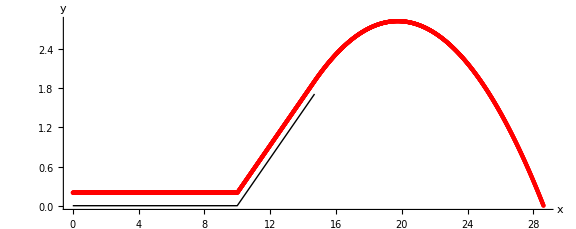

```mathematica
g=9.81;
kot=20 Degree;
dRavnina=10;
dKlanec=5;
r=0.2;
v0={11.,0.}; 
deltaT=0.001;


naKlancu[{x_,y_}]:=x>dRavnina&&x<=dRavnina+dKlanec*Cos[kot]

hitrostNaKlanec[v_,a_]:={v[[1]]*Cos[a],Abs[v[[1]]*Sin[a]]}

posodobiHitrostKlanec[v_,a_,dt_]:=Module[{aGrav=g*Sin[a],smer={Cos[a],Sin[a]}},v+aGrav*dt*smer]

posodobiHitrostPosevniMet[v_,dt_]:={v[[1]],v[[2]]-g*dt}

posodobiLego[r_,v_,dt_]:=r+dt*v

lega={0.,r};
hitrost=v0;
seznamLeg={lega};
naKlanecPresel=False;

While[lega[[2]]>0,If[lega[[1]]<dRavnina,Null,If[naKlancu[lega],If[!naKlanecPresel,hitrost=hitrostNaKlanec[hitrost,kot];
naKlanecPresel=True;];
hitrost=posodobiHitrostKlanec[hitrost,kot,deltaT],hitrost=posodobiHitrostPosevniMet[hitrost,deltaT]]];
lega=posodobiLego[lega,hitrost,deltaT];
AppendTo[seznamLeg,lega];]

Graphics[{Red,PointSize[Small],Point/@seznamLeg,Black,Line[{{0,0},{dRavnina,0},{dRavnina+dKlanec*Cos[kot],dKlanec*Sin[kot]}}]},Axes->True,AspectRatio->0.4,PlotRange->All,AxesLabel->{"x","y"},ImageSize->Large]
```